## Probability of resistance for the LG model with constant rates

```mathematica
<<MaTeX`
```

```mathematica
If[loopcount>1,Clear@@DeleteCases[Names@"`*","loopcount"|"file"]];
If[Head[loopcount]==Symbol, loopcount=1;]
```

```mathematica
(*$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`50."&);*)
```

### Input

```mathematica
minp=1.4 10^3+1;dp=1;maxp =1.5 10^3;

minT=35;
dT =1;maxT=35;
```

#### Constant rates

```mathematica
dS=0.1;
dA=0.1;
dB=0.1;
dD=0.1;
ρS=1.0-dS;
ρA=1.1-dA;
ρB=1.2-dB;
ρD=1.3-dD;
μA=1.0 10^-3;
μB=1.0 10^-4;
n0=10^3;
kS=minp +  dp*(loopcount-1);
kA=1.1 10^3;
kB=1.2 10^3;
kD= 1.3 10^3;tmax = 150;
```

### Single resistance

#### Mean values & P_ext

```mathematica
nS[t_]:=kS/(1+(kS/n0-1)Exp[-ρS(1-μA-μB) t]);Pext[t_,T_,ki_,dib_,rib_]:=(dib/ki((T-t)-(ki-1)/rib(Exp[-rib(T-t)]-1)))/(dib/ki((T-t)-(ki-1)/rib(Exp[-rib(T-t)]-1))+1);(*b is for bar*)
nAsol=NDSolve[{n'[t]==(dS+ρS(1-nS[t]/kS))μA nS[t]+ρA(1-μB)(1-n[t]/kA)n[t],n[0]==0},n,{t,0,tmax}];
{nA}=nAsol[[1,All,2]];
nBsol=NDSolve[{n'[t]==(dS+ρS(1-nS[t]/kS))μB nS[t]+ρB(1-μA)(1-n[t]/kB)n[t],n[0]==0},n,{t,0,tmax}];
{nB}=nBsol[[1,All,2]];
```

#### P_R^single

```mathematica
WAB[t_,μi_]:=(dS+ρS(1-nS[t]/kS))μi nS[t];
PhiA[T_]:=NIntegrate[WAB[t,μA](Pext[t,T,kA,dA(1-μB),ρA(1-μB)]-1),{t,0,T}];
PhiB[T_]:=NIntegrate[WAB[t,μB](Pext[t,T,kB,dB(1-μA),ρB(1-μA)]-1),{t,0,T}];
PRSingle[T_]:=1-Exp[PhiA[T]+PhiB[T]];
```

#### Save data

```mathematica
SetDirectory[NotebookDirectory[]];
filename = "non-int-log-param-7-kS-PRS-T=35";
If[loopcount==1, Print["Total number of iterations: ",  (maxp-minp)/dp+1];(*DeleteFile[StringJoin[filename,".txt"]];*)file=OpenAppend[StringJoin[filename,".txt"]];];
Quiet[dataTable=Table[PRSingle[T],{T,minT,maxT, dT}];]
Do[WriteString[file,StringJoin[ToString[dataTable[[i]], InputForm]],"\t"],{i,1,Length[dataTable]}];
WriteString[file,"\n"];
If[Mod[loopcount,10]==0,Print["iteration: ", loopcount]];
loopcount+=1; 
If[loopcount==(maxp-minp)/dp+2,Export[FileNameJoin[{Directory[],StringJoin[filename,"-time",".txt"]}],Table[T,{T,minT,maxT, dT}],"Table","FieldSeparators"->" "];
Export[FileNameJoin[{Directory[],StringJoin[filename,"-parameter",".txt"]}],Table[p,{p,minp,maxp, dp}],"Table","FieldSeparators"->" "];Close[file];]
If[ loopcount <= (maxp-minp)/dp+1,NotebookEvaluate@EvaluationNotebook[]];
```

Total number of iterations: 100.

iteration: 10

iteration: 20

iteration: 30

iteration: 40

iteration: 50

iteration: 60

iteration: 70

iteration: 80

iteration: 90

iteration: 100

### Double resistance

#### Mean values & P_ext

```mathematica
(*nS[t_]:=kS/(1+(kS/n0-1)Exp[-ρS(1-μA-μB) t]);Pext[t_,T_,ki_,dib_,rib_]:=(dib/ki((T-t)-(ki-1)/rib(Exp[-rib(T-t)]-1)))/(dib/ki((T-t)-(ki-1)/rib(Exp[-rib(T-t)]-1))+1);(*b is for bar*)
nAsol=NDSolve[{n'[t]==(dS+ρS(1-nS[t]/kS))μA nS[t]+ρA(1-μB)(1-n[t]/kA)n[t],n[0]==0},n,{t,0,tmax}];
{nA}=nAsol[[1,All,2]];
nBsol=NDSolve[{n'[t]==(dS+ρS(1-nS[t]/kS))μB nS[t]+ρB(1-μA)(1-n[t]/kB)n[t],n[0]==0},n,{t,0,tmax}];
{nB}=nBsol[[1,All,2]];*)
```

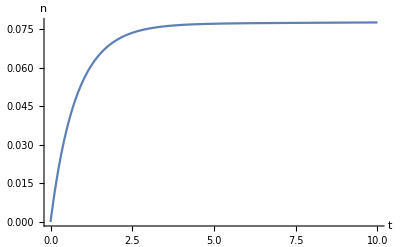

```mathematica
Plot[{Pext[0,T,kD,dD,ρD]},{T,0,10},PlotRange->All,AxesLabel->{"t","n"}]
```

#### P_R^double

```mathematica
(*WD[t_]:=(dA + ρA(1-nA[t]/kA))μB nA[t] + (dB + ρB(1-nB[t]/kB))μA nB[t];
PhiD[T_]:=NIntegrate[WD[t](Pext[t,T,kD,dD,ρD]-1),{t,0,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3];
PRDouble[T_]:=1-Exp[PhiD[T]];*)
```

#### Save data

```mathematica
(*SetDirectory[NotebookDirectory[]];
filename = "non-int-log-param-7-kS-PRS-T=35";
If[loopcount==1, Print["Total number of iterations: ",  (maxp-minp)/dp+1];(*DeleteFile[StringJoin[filename,".txt"]];*)file=OpenAppend[StringJoin[filename,".txt"]];]
Quiet[dataTable=Table[PRDouble[T],{T,minT,maxT, dT}];]
Do[WriteString[file,StringJoin[ToString[dataTable[[i]], InputForm]],"\t"],{i,1,Length[dataTable]}];
WriteString[file,"\n"];
If[Mod[loopcount,10]==0,Print["iteration: ", loopcount]];
loopcount+=1; 
If[loopcount==(maxp-minp)/dp+2,Export[FileNameJoin[{Directory[],StringJoin[filename,"-time",".txt"]}],Table[T,{T,minT,maxT, dT}],"Table","FieldSeparators"->" "];
Export[FileNameJoin[{Directory[],StringJoin[filename,"-parameter",".txt"]}],Table[p,{p,minp,maxp, dp}],"Table","FieldSeparators"->" "];Close[file];]
If[ loopcount <= (maxp-minp)/dp+1,NotebookEvaluate@EvaluationNotebook[]];*)
```